```mathematica
(*
[HW06] PIVOT GEOMETRY PRACTICE
*)
```

```mathematica
(*
PIVOT ALGORITHM
*)
pivot[iStar_,jStar_,tab_]:=(
nRows=Dimensions[tab][[1]];
nCols=Dimensions[tab][[2]];
newTab=tab;
newTab[[1,jStar]]=tab[[iStar,nCols]];
newTab[[iStar,nCols]]=tab[[1,jStar]];
For[ii=2,ii<=nRows,ii++,
For[jj=1,jj<nCols,jj++,
If[ii==iStar&&jj==jStar,newTab[[ii,jj]]=1/tab[[iStar,jStar]]];
If[ii==iStar&&jj!=jStar,newTab[[ii,jj]]=-tab[[ii,jj]]/tab[[iStar,jStar]]];
If[ii!=iStar&&jj==jStar,newTab[[ii,jj]]=tab[[ii,jj]]/tab[[iStar,jStar]]];
If[ii!=iStar&&jj!=jStar,newTab[[ii,jj]]=tab[[ii,jj]]-tab[[iStar,jj]]*tab[[ii,jStar]]/tab[[iStar,jStar]]];
];
];
Return[newTab]
)
```

```mathematica
(*"
min z = -2x1 - 4x2 + 4
   g1 = 4x1 + 3x2 <= 48
   g2 = 4x1 + 3x2 >= 24
   g3 = 3x1 - 1x2 >= -6
   g4 = 3x1 - 1x2 <=  6
"*)
```

```mathematica
(*"
Define the
  1) objective function
2) constraint functions
3) constants
4) slack functions
"*)
Clear[z,g1,g2,g3,g4,s1,s2,s3,s4]
z[x1_,x2_]:=-2x1-4x2+4;
g1[x1_,x2_]:=4x1 + 3x2;
g2[x1_,x2_]:=4x1 + 3x2;
g3[x1_,x2_]:=3x1 - 1x2 ;
g4[x1_,x2_]:=3x1 - 1x2 ;
b1=48;
b2=24;
b3=-6;
b4=6;
s1[x1_,x2_]:=-g1[x1,x2]+b1;
s2[x1_,x2_]:=g2[x1,x2]-b2;
s3[x1_,x2_]:=g3[x1,x2]-b3;
s4[x1_,x2_]:=-g4[x1,x2]+b4;
```

```mathematica
(* solve for the constraint boundaries *)
g1[x1_]=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]];
g2[x1_]=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]];
g3[x1_]=x2/.Solve[g3[x1,x2]==b3,{x2}][[1,1]];
g4[x1_]=x2/.Solve[g4[x1,x2]==b4,{x2}][[1,1]];
```

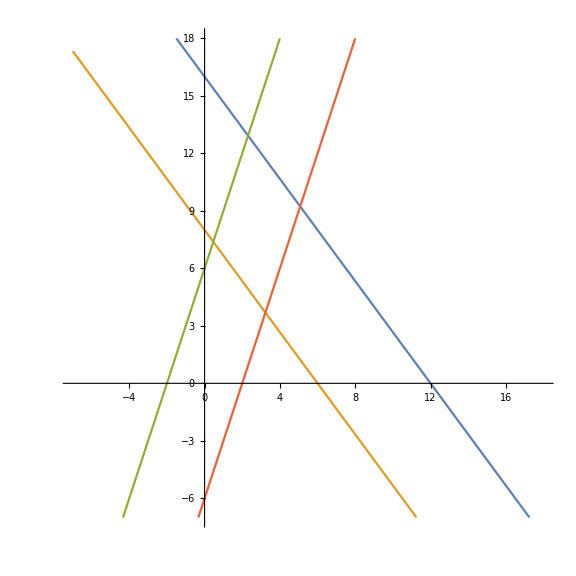

```mathematica
(* plot the constraint boundaries *)
Plot[
{g1[x],g2[x],g3[x],g4[x]},
{x,-7,18},
AspectRatio->Automatic,
ImageSize->Large,
PlotRange->{-7,18}
]
```

```mathematica
(*
[A]
*)
a0={"x1","x2",1,""};
a1={-4,-3,48,"s1"};
a2={4,3,-24,"s2"};
a3={3,-1,6,"s3"};
a4={-3,1,6,"s4"};
aobj={-2,-4,4,"z->min"};
a={a0,a1,a2,a3,a4,aobj};
Print["a = ",MatrixForm[a]]
```

a = (x1 | x2 | 1 | 
-4 | -3 | 48 | s1
4 | 3 | -24 | s2
3 | -1 | 6 | s3
-3 | 1 | 6 | s4
-2 | -4 | 4 | z->min)

```mathematica
(*
[A] BASIC SOLUTION
*)
x1=0;
x2=0;
zz=4;
ss1=48;
ss2=-24;
ss3=6;
ss4=6;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 0 x2 = 0 z = 4

True,True,True,True,True

```mathematica
(*
[B]
*)
b=pivot[4,1,a];
Print["b = ",MatrixForm[b]]
```

b = (s3 | x2 | 1 | 
-4/3 | -13/3 | 56 | s1
4/3 | 13/3 | -32 | s2
1/3 | 1/3 | -2 | x1
-1 | 0 | 12 | s4
-2/3 | -14/3 | 8 | z->min)

```mathematica
(*
[B] BASIC SOLUTION
*)
x1=-2;
x2=0;
zz=8;
ss1=56;
ss2=-32;
ss3=0;
ss4=12;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = -2 x2 = 0 z = 8

True,True,True,True,True

```mathematica
(*
[C]
*)
c=pivot[3,2,b];
Print["c = ",MatrixForm[c]]
```

c = (s3 | s2 | 1 | 
0 | -1 | 24 | s1
-4/13 | 3/13 | 96/13 | x2
3/13 | 1/13 | 6/13 | x1
-1 | 0 | 12 | s4
10/13 | -14/13 | -344/13 | z->min)

```mathematica
(*
[C] BASIC SOLUTION
*)
x1=6/13;
x2=96/13;
zz=-344/13;
ss1=24;
ss2=0;
ss3=0;
ss4=12;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 6/13 x2 = 96/13 z = -344/13

True,True,True,True,True

```mathematica
(*
[D]
*)
d=pivot[2,2,c];
Print["d = ",MatrixForm[d]]
```

d = (s3 | s1 | 1 | 
0 | -1 | 24 | s2
-4/13 | -3/13 | 168/13 | x2
3/13 | -1/13 | 30/13 | x1
-1 | 0 | 12 | s4
10/13 | 14/13 | -680/13 | z->min)

```mathematica
(*
[D] BASIC SOLUTION
*)
x1=30/13;
x2=168/13;
zz=-680/13;
ss1=0;
ss2=24;
ss3=0;
ss4=12;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 30/13 x2 = 168/13 z = -680/13

True,True,True,True,True

```mathematica
(*
[E]
*)
e=pivot[5,1,d];
Print["e = ",MatrixForm[e]]
```

e = (s4 | s1 | 1 | 
0 | -1 | 24 | s2
4/13 | -3/13 | 120/13 | x2
-3/13 | -1/13 | 66/13 | x1
-1 | 0 | 12 | s3
-10/13 | 14/13 | -560/13 | z->min)

```mathematica
(*
[E] BASIC SOLUTION
*)
x1=66/13;
x2=120/13;
zz=-560/13;
ss1=0;
ss2=24;
ss3=12;
ss4=0;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 66/13 x2 = 120/13 z = -560/13

True,True,True,True,True

```mathematica
(*
[F]
*)
f=pivot[2,2,e];
Print["f = ",MatrixForm[f]]
```

f = (s4 | s2 | 1 | 
0 | -1 | 24 | s1
4/13 | 3/13 | 48/13 | x2
-3/13 | 1/13 | 42/13 | x1
-1 | 0 | 12 | s3
-10/13 | -14/13 | -224/13 | z->min)

```mathematica
(*
[F] BASIC SOLUTION
*)
x1=42/13;
x2=48/13;
zz=-224/13;
ss1=24;
ss2=0;
ss3=12;
ss4=0;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 42/13 x2 = 48/13 z = -224/13

True,True,True,True,True

```mathematica
(*
[G]
*)
g=pivot[3,1,f];
Print["g = ",MatrixForm[g]]
```

g = (x2 | s2 | 1 | 
0 | -1 | 24 | s1
13/4 | -3/4 | -12 | s4
-3/4 | 1/4 | 6 | x1
-13/4 | 3/4 | 24 | s3
-5/2 | -1/2 | -8 | z->min)

```mathematica
(*
[G] BASIC SOLUTION
*)
x1=6;
x2=0;
zz=-8;
ss1=24;
ss2=0;
ss3=24;
ss4=-12;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 6 x2 = 0 z = -8

True,True,True,True,True

```mathematica
(*
[H]
*)
h=pivot[3,2,g];
Print["h = ",MatrixForm[h]]
```

h = (x2 | s4 | 1 | 
-13/3 | 4/3 | 40 | s1
13/3 | -4/3 | -16 | s2
1/3 | -1/3 | 2 | x1
0 | -1 | 12 | s3
-14/3 | 2/3 | 0 | z->min)

```mathematica
(*
[H] BASIC SOLUTION
*)
x1=2;
x2=0;
zz=0;
ss1=40;
ss2=-16;
ss3=12;
ss4=0;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 2 x2 = 0 z = 0

True,True,True,True,True

```mathematica
(*
[I]
*)
i=pivot[2,2,h];
Print["i = ",MatrixForm[i]]
```

i = (x2 | s1 | 1 | 
13/4 | 3/4 | -30 | s4
0 | -1 | 24 | s2
-3/4 | -1/4 | 12 | x1
-13/4 | -3/4 | 42 | s3
-5/2 | 1/2 | -20 | z->min)

```mathematica
(*
[I] BASIC SOLUTION
*)
x1=12;
x2=0;
zz=-20;
ss1=0;
ss2=24;
ss3=42;
ss4=-30;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 12 x2 = 0 z = -20

True,True,True,True,True

```mathematica
(*
[J]
*)
j=pivot[4,1,i];
Print["j = ",MatrixForm[j]]
```

j = (x1 | s1 | 1 | 
-13/3 | -1/3 | 22 | s4
0 | -1 | 24 | s2
-4/3 | -1/3 | 16 | x2
13/3 | 1/3 | -10 | s3
10/3 | 4/3 | -60 | z->min)

```mathematica
(*
[J] BASIC SOLUTION
*)
x1=0;
x2=16;
zz=-60;
ss1=0;
ss2=24;
ss3=-10;
ss4=22;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 0 x2 = 16 z = -60

True,True,True,True,True

```mathematica
(*
[K]
*)
k=pivot[3,2,j];
Print["k = ",MatrixForm[k]]
```

k = (x1 | s2 | 1 | 
-13/3 | 1/3 | 14 | s4
0 | -1 | 24 | s1
-4/3 | 1/3 | 8 | x2
13/3 | -1/3 | -2 | s3
10/3 | -4/3 | -28 | z->min)

```mathematica
(*
[K] BASIC SOLUTION
*)
x1=0;
x2=8;
zz=-28;
ss1=24;
ss2=0;
ss3=-2;
ss4=14;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 0 x2 = 8 z = -28

True,True,True,True,True

```mathematica
(*
[L]
*)
l=pivot[2,2,k];
Print["l = ",MatrixForm[l]]
```

l = (x1 | s4 | 1 | 
13 | 3 | -42 | s2
-13 | -3 | 66 | s1
3 | 1 | -6 | x2
0 | -1 | 12 | s3
-14 | -4 | 28 | z->min)

```mathematica
(*
[L] BASIC SOLUTION
*)
x1=0;
x2=-6;
zz=28;
ss1=66;
ss2=-42;
ss3=12;
ss4=0;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 0 x2 = -6 z = 28

True,True,True,True,True

```mathematica
(*"
min z = -2u1 + 2u2 - 4u3 + 4u4 + 4
   g1 =  4u1 - 4u2 + 3u3 - 3u4 <= 48
   g2 =  4u1 - 4u2 + 3u3 - 3u4 >= 24
   g3 =  3u1 - 3u2 - 1u3 + 1u4 >= -6
   g4 =  3u1 - 3u2 - 1u3 + 1u4 <=  6
"*)
```

```mathematica
(*
[A]
*)
a0={"u1","u2","u3","u4",1,""};
a1={-4,4,-3,3,48,"s1"};
a2={4,-4,3,-3,-24,"s2"};
a3={3,-3,-1,1,6,"s3"};
a4={-3,3,1,-1,6,"s4"};
aobj={-2,2,-4,-4,4,"z->min"};
a={a0,a1,a2,a3,a4,aobj};
Print["a = ",MatrixForm[a]]
```

a = (u1 | u2 | u3 | u4 | 1 | 
-4 | 4 | -3 | 3 | 48 | s1
4 | -4 | 3 | -3 | -24 | s2
3 | -3 | -1 | 1 | 6 | s3
-3 | 3 | 1 | -1 | 6 | s4
-2 | 2 | -4 | -4 | 4 | z->min)

```mathematica
(*
[A] BASIC SOLUTION
*)
u1=0;
u2=0;
u3=0;
u4=0;
x1=u1-u2;
x2=u3-u4;
zz=4;
ss1=48;
ss2=-24;
ss3=6;
ss4=6;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 0 x2 = 0 z = 4

True,True,True,True,True

```mathematica
(*
[B]
*)
b=pivot[4,2,a];
Print["b = ",MatrixForm[b]]
```

b = (u1 | s3 | u3 | u4 | 1 | 
0 | -4/3 | -13/3 | 13/3 | 56 | s1
0 | 4/3 | 13/3 | -13/3 | -32 | s2
1 | -1/3 | -1/3 | 1/3 | 2 | u2
0 | -1 | 0 | 0 | 12 | s4
0 | -2/3 | -14/3 | -10/3 | 8 | z->min)

```mathematica
(*
[B] BASIC SOLUTION
*)
u1=0;
u2=2;
u3=0;
u4=0;
x1=u1-u2;
x2=u3-u4;
zz=8;
ss1=56;
ss2=-32;
ss3=0;
ss4=12;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = -2 x2 = 0 z = 8

True,True,True,True,True

```mathematica
(*
[BC]
*)
bc=pivot[4,3,b];
Print["bc = ",MatrixForm[bc]]
```

bc = (u1 | s3 | u2 | u4 | 1 | 
-13 | 3 | 13 | 0 | 30 | s1
13 | -3 | -13 | 0 | -6 | s2
3 | -1 | -3 | 1 | 6 | u3
0 | -1 | 0 | 0 | 12 | s4
-14 | 4 | 14 | -8 | -20 | z->min)

```mathematica
(*
[BC] BASIC SOLUTION
*)
u1=0;
u2=0;
u3=6;
u4=0;
x1=u1-u2;
x2=u3-u4;
zz=-20;
ss1=30;
ss2=-6;
ss3=0;
ss4=12;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 0 x2 = 6 z = -20

True,True,True,True,True

```mathematica
(*
[C]
*)
d=pivot[3,1,c];
Print["d = ",MatrixForm[d]]
```

d = (s2 | s3 | u2 | u4 | 1 | 
-1 | 0 | 0 | 0 | 24 | s1
1/13 | 3/13 | 1 | 0 | 6/13 | u1
3/13 | -4/13 | 0 | 1 | 96/13 | u3
0 | -1 | 0 | 0 | 12 | s4
-14/13 | 10/13 | 0 | -8 | -344/13 | z->min)

```mathematica
(*
[C] BASIC SOLUTION
*)
u1=6/13;
u2=0;
u3=96/13;
u4=0;
x1=u1-u2;
x2=u3-u4;
zz=-344/13;
ss1=24;
ss2=0;
ss3=0;
ss4=12;

Print["x1 = ",x1," x2 = ",x2," z = ",zz]

Print[
s1[x1,x2]==ss1,",",
s2[x1,x2]==ss2,",",
s3[x1,x2]==ss3,",",
s4[x1,x2]==ss4,",",
z[x1,x2]==zz]
```

x1 = 6/13 x2 = 96/13 z = -344/13

True,True,True,True,True

```mathematica
(*
[D]
*)
d=pivot[3,1,c];
Print["d = ",MatrixForm[d]]
```

d = (s2 | s3 | u2 | u4 | 1 | 
-1 | 0 | 0 | 0 | 24 | s1
1/13 | 3/13 | 1 | 0 | 6/13 | u1
3/13 | -4/13 | 0 | 1 | 96/13 | u3
0 | -1 | 0 | 0 | 12 | s4
-14/13 | 10/13 | 0 | -8 | -344/13 | z->min)